Gri

```mathematica
ptMin=0;
ptMax=3;
noPts =5;
width=(ptMax-ptMin)/(noPts-1)//N
```

0.75

Read grid

```mathematica
SetDirectory[NotebookDirectory[]];
grid=Import["test_1d.txt","Table"];
```

Evaluate

```mathematica
xPt=2.22;
idx=IntegerPart[xPt/width]
```

2

```mathematica
secStart=ptMin+idx*width
secEnd=secStart+width
```

1.5

2.25

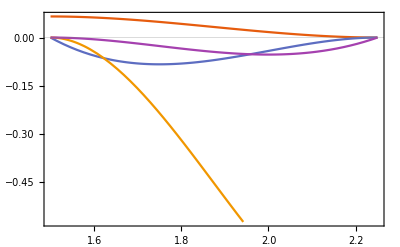

```mathematica
Plot[Evaluate[{grid[[idx+1,2]]*(1-3 x^2+2 x^3),grid[[idx+1,3]]*(x-2 x^2+x^3),grid[[idx+2,2]]*(3 x^2-2 x^3),grid[[idx+2,3]]*(-(x^2-x^3))}/.x->(xVal-secStart)/(secEnd-secStart)],{xVal,secStart,secEnd}]
```

```mathematica
vals=Evaluate[{grid[[idx+1,2]]*(1-3 x^2+2 x^3),grid[[idx+1,3]]*(x-2 x^2+x^3),grid[[idx+2,2]]*(3 x^2-2 x^3),grid[[idx+2,3]]*(-(x^2-x^3))}/.x->(xVal-secStart)/(secEnd-secStart)]/.xVal->xPt
```

{0.000306177,-0.000863358,-0.901679,-0.0131873}

```mathematica
Total[vals]
```

-0.915423